## Luminance

#### from RGB

```mathematica
{r,g,b}=ColorSeparate[-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
L=0.3*r+0.59*g+0.11*b
```

-Graphics-

#### from HSV

```mathematica
ColorSeparate[ColorConvert[-Graphics-,"HSB"]][[3]]
```

-Graphics-

### Brightness

#### Automatic Equalization

```mathematica
BrightnessEqualize[-Graphics-]
```

-Graphics-

#### Scale a factor

```mathematica
-Graphics-*1.2
```

-Graphics-

### Contrast

```mathematica
dL=ImageData[L,DataReversed->True];
Graphics[Raster[dL]]
```

-Graphics-

```mathematica
mL=dL-Mean[dL//Flatten]+1.2;
Graphics@Raster@mL
```

-Graphics-

```mathematica
raw=ImageData[-Graphics-,DataReversed->True];
```

```mathematica
Graphics[Raster[raw*mL]]
```

-Graphics-

### Histogram Equalization

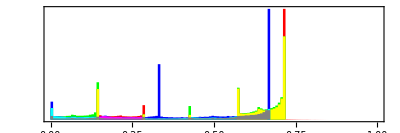

```mathematica
ImageHistogram[-Graphics-]
```

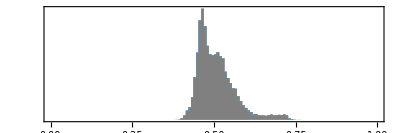
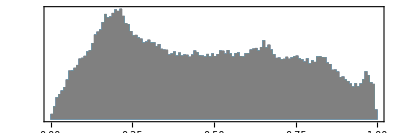

```mathematica
{ImageHistogram[-Graphics-],ImageHistogram[-Graphics-]}
```

```mathematica
HistogramTransform[-Graphics-]
```

-Graphics-

## Color

### Gray Scale

```mathematica
ColorConvert[-Graphics-,"Grayscale"]
```

-Graphics-

### Saturation

```mathematica
Table[ColorCombine[{#[[1]],#[[2]]*f,#[[3]]},"HSB"]&@ColorSeparate[ColorConvert[-Graphics-,"HSB"]],{f,0,2,0.4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorConvert[-Graphics-,"Grayscale"]
```

-Graphics-

### White Balance

#### Automatic White Balance

```mathematica
{-Graphics-,ColorBalance[-Graphics-]}
```

{-Graphics-,-Graphics-}

```mathematica
WhitePoint[-Graphics-]
```

WhitePoint[-Graphics-]

```mathematica
ChromaticityPlot["sRGB",WhitePoint->Automatic]
```

-Graphics-

#### Von Kries method: adjust colors in LMS color space

```mathematica
data=ImageData[-Graphics-,DataReversed->True];
Graphics[Raster[data]]
```

-Graphics-

```mathematica
RGBtoXYZ={{0.4124,0.3576,0.1804},{0.2126,0.7152,0.0722},{0.0193,0.1192,0.9502}};
RGBtoXYZ//MatrixForm
invXYZ = Inverse[RGBtoXYZ]
```

(0.4124 | 0.3576 | 0.1804
0.2126 | 0.7152 | 0.0722
0.0193 | 0.1192 | 0.9502)

{{3.24064,-1.53724,-0.498444},{-0.968935,1.87577,0.0414282},{0.0557281,-0.204087,1.05734}}

```mathematica
XYZtoLMS={{0.40024,0.7076,-0.08081},{-0.2263,1.16532,0.0457},{0,0,0.91822}};
XYZtoLMS//MatrixForm
invLMS=Inverse[XYZtoLMS]
```

(0.40024 | 0.7076 | -0.08081
-0.2263 | 1.16532 | 0.0457
0 | 0 | 0.91822)

{{1.85994,-1.12938,0.219897},{0.361191,0.638812,-6.3706×10^-6},{0.,0.,1.08906}}

```mathematica
{w,h,c}=Dimensions@data
```

{387,521,3}

```mathematica
LMSdata=Table[XYZtoLMS.RGBtoXYZ.data[[x,y,;;]],{x,w},{y,h}];
Graphics[Raster[LMSdata]]
```

-Graphics-

```mathematica
white=Nearest[Flatten[LMSdata,1],{1,1,1},1]//Flatten
```

{0.952267,0.933125,0.710098}

```mathematica
result=Table[invXYZ.invLMS.(LMSdata[[x,y,;;]]/white),{x,w},{y,h}];
Graphics[Raster[result]]
```

-Graphics-

```mathematica
{Graphics[Raster[result]],ColorBalance[-Graphics-,Method->"LMSScaling"]}
```

{-Graphics-,-Graphics-}